```mathematica
NUnitTheory = 8;
NverticalTheoryZ = 8;
res = NUnitTheory;

fermiArc1ks = Table[{π/2,kx},{kx,0,π,(2π)/NUnitTheory}];
fermiArc2ks = Table[{π/2,kx},{kx,π,2π,(2π)/NUnitTheory}];

Frequency = 2.2*10^6;
Omega = 2*π*Frequency;
LBZ = 27*10^-6;
C1 = Omega*150*10^-12;
CAz = C1;
Cy = C1/2;
Ry = 270;
alpha = -Omega/(Omega^2*LBZ);

Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi[[Mu+1]]
```

```mathematica
HcOBC[{kx_,ky_},z_]:=Sum[1/NverticalTheoryZ *((-(CAz+alpha)Cos[ky]) X[0]-(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])) X[1]-C1 Sin[kz] X[2]-(CAz-alpha) Cos[ky] X[3])*Exp[I*kz*z],{kz,0,(NverticalTheoryZ-1)2π/NverticalTheoryZ,2π/NverticalTheoryZ}]

HcOBCMatrix[kx_,ky_] :=ArrayFlatten[Table[Which[xpos == ypos,HcOBC[{kx,ky},0],xpos == ypos +1,HcOBC[{kx,ky},1],xpos == ypos-1,HcOBC[{kx,ky},-1],True,0],{xpos,1,NverticalTheoryZ},{ypos,1,NverticalTheoryZ}]];

HcOBCMatrixSortedEigensystem[kx_,ky_] := Block[{unsortedEigensystem=Eigensystem[HcOBCMatrix[kx,ky]]},unsortedEigensystem[[;;,Ordering[unsortedEigensystem[[1]]]]]];

HcOBCMatrixUnsortedEigensystem[kx_,ky_] := Eigensystem[HcOBCMatrix[kx,ky]];

HcOBCSortedEigenstateContributionsColor[state_,sub_]:=Block[{normStateTheory = Normalize[state]},
(Abs[state⟦If[sub==1,1,-1]⟧]/(∑_(i=2 NverticalTheoryZ)^(2 NverticalTheoryZ) Abs[state⟦i⟧]))];
```

```mathematica
fermiArc1Loc =Table[
Sum[(Abs[(HcOBCMatrixUnsortedEigensystem[i[[1]],i[[2]]][[2,-(3-sub)]])[[k]]])^4,{k,1,Length[HcOBCMatrixUnsortedEigensystem[i[[1]],i[[2]]][[2,-(3-sub)]]]}]/Sum[(Abs[(HcOBCMatrixUnsortedEigensystem[i[[1]],i[[2]]][[2,-(3-sub)]])[[k]]])^2,{k,1,Length[HcOBCMatrixUnsortedEigensystem[i[[1]],i[[2]]][[2,-(3-sub)]]]}]
,{i,fermiArc2ks},{sub,1,2}];
```

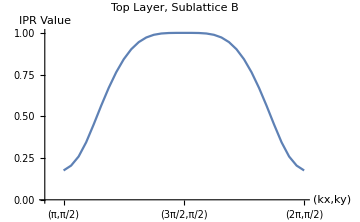
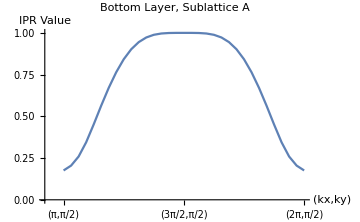
-Graphics- | -Graphics-
 |

```mathematica
Grid[{{ListLinePlot[fermiArc1Loc[[;;,1]],Ticks->{{{1,"(π,π/2)"},{res/4+1,"(3π/2,π/2)"},{res/2+1,"(2π,π/2)"}},Automatic},AxesOrigin->{-1.5,0},PlotRange->Full,AxesLabel->{"(kx,ky)","IPR Value"},PlotLabel->"Top Layer, Sublattice B",ImageSize->Medium]
,
ListLinePlot[fermiArc1Loc[[;;,2]],Ticks->{{{1,"(π,π/2)"},{res/4+1,"(3π/2,π/2)"},{res/2+1,"(2π,π/2)"}},Automatic},AxesOrigin->{-1.5,0},PlotRange->Full,AxesLabel->{"(kx,ky)","IPR Value"},PlotLabel->"Bottom Layer, Sublattice A",ImageSize->Medium]},{}}]
```

```mathematica
OBCDispersion = Table[SortBy[Eigenvalues[HcOBCMatrix[kx,ky]][[-2;;-1]],Re],{kx,0,π,2π/NUnitTheory},{ky,π,2π,2π/NUnitTheory}];
```

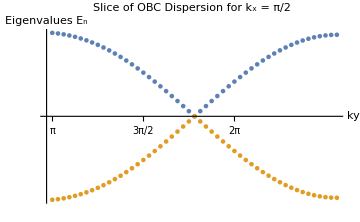
|  | 
-Graphics3D- |  | -Graphics-

```mathematica
Grid[{{},{ListPlot3D[{OBCDispersion[[;;,;;,1]],OBCDispersion[[;;,;;,2]]},AxesLabel->{"ky","kx",Rotate["Eigenvalues  \!\(\*SubscriptBox[\(E\), \(n\)]\)",π/2]},Ticks->{{{1,"π"},{res/4+1,"3π/2"},{res/2+1,"2π"}},{{1,"0"},{res/4+1,"π/2"},{res/2+1,"π"}},Automatic},ImageSize->Medium,PlotLabel->"OBC Dispersion Around a Fermi Arc"],"",ListPlot[{OBCDispersion[[NUnitTheory/2-1,;;,2]],OBCDispersion[[NUnitTheory/2-1,;;,1]]},AxesLabel->{"ky","Eigenvalues  \!\(\*SubscriptBox[\(E\), \(n\)]\)"},Ticks->{{{1,"π"},{res/4+1,"3π/2"},{res/2+1,"2π"}},{{1,"0"},{res/4+1,"π/2"},{res/2+1,"π"}},Automatic},ImageSize->Medium,PlotLabel->"Slice of OBC Dispersion for k_x = π/2"]}}]
```

```mathematica
PathCoordXTheory=Join[Subdivide[0,0,2],Subdivide[π/4,π,3],Subdivide[π,π,3],Subdivide[(5 π)/4,2 π,3],Subdivide[2 π,2 π,1]];
PathCoordYTheory=Join[Subdivide[2 π,(3 π)/2,2],Subdivide[(3 π)/2,(3 π)/2,3],Subdivide[(7 π)/4,2 π,1],Subdivide[π/4,π/2,1],Subdivide[π/2,π/2,3],Subdivide[π/4,0,1]];

p1Theory=1;
p2Theory=1+(Abs[2 π-(3 π)/2] NUnitTheory)/(2 π);
p3Theory=1+(Abs[2 π-(3 π)/2] NUnitTheory)/(2 π)+(Abs[π-(2 π)/NUnitTheory] NUnitTheory)/(2 π)+1;
p4Theory=1+(Abs[2 π-(3 π)/2] NUnitTheory)/(2 π)+(Abs[π-(2 π)/NUnitTheory] NUnitTheory)/(2 π)+(Abs[(3 π)/2+(2 π)/NUnitTheory-2 π] NUnitTheory)/(2 π)+(Abs[(2 π)/NUnitTheory-π/2] NUnitTheory)/(2 π)+1+2;
p5Theory=1+(Abs[2 π-(3 π)/2] NUnitTheory)/(2 π)+(Abs[π-(2 π)/NUnitTheory] NUnitTheory)/(2 π)+(Abs[(3 π)/2+(2 π)/NUnitTheory-2 π] NUnitTheory)/(2 π)+(Abs[(2 π)/NUnitTheory-π/2] NUnitTheory)/(2 π)+1+(Abs[(2 π)/2+(2 π)/NUnitTheory-2 π] NUnitTheory)/(2 π)+3;
p6Theory=1+(Abs[2 π-(3 π)/2] NUnitTheory)/(2 π)+(Abs[π-(2 π)/NUnitTheory] NUnitTheory)/(2 π)+(Abs[(3 π)/2+(2 π)/NUnitTheory-2 π] NUnitTheory)/(2 π)+(Abs[(2 π)/NUnitTheory-π/2] NUnitTheory)/(2 π)+1+(Abs[(2 π)/2+(2 π)/NUnitTheory-2 π] NUnitTheory)/(2 π)+(Abs[π/2-(2 π)/NUnitTheory] NUnitTheory)/(2 π)+4;
```

```mathematica
frequency = 2.2*10^6;

L1Value = 27*10^-6;
L2Value = 5.6*10^-6;
L3Value = 27*10^-6;

C1Value = 150*10^-12;
C2Value = 75*10^-12;
C3Value = 150*10^-12;

Omega = 2*π*frequency;
LBZ = L1Value;
C1 = Omega*C1Value;
CAz = C1;
Cy = C1/2;
Alpha = Omega/(Omega^2*LBZ);

Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi⟦Mu+1⟧

HcOBC[{kx_,ky_},z_]:=Sum[1/NverticalTheoryZ N[(-(CAz-Alpha)Cos[ky]) X[0]-(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])) X[1]-C1 Sin[kz] X[2]-(CAz+Alpha) Cos[ky] X[3]]Exp[ⅈ kz z],{kz,0,((NverticalTheoryZ-1) 2 π)/NverticalTheoryZ,(2 π)/NverticalTheoryZ}]

HcOBCMatrix[kx_,ky_]:=ArrayFlatten[Table[Which[xpos==ypos,HcOBC[{kx,ky},0],xpos==ypos+1,HcOBC[{kx,ky},1],xpos==ypos-1,HcOBC[{kx,ky},-1],True,0],{xpos,1,NverticalTheoryZ},{ypos,1,NverticalTheoryZ}]];

HcOBCMatrixSortedEigensystem[kx_,ky_]:=Block[{unsortedEigensystem=Eigensystem[HcOBCMatrix[kx,ky]]},unsortedEigensystem⟦1;;All,Ordering[unsortedEigensystem⟦1⟧]⟧];

HcIPR[state_]:=RGBColor[((∑_(i=1)^(2 NverticalTheoryZ) Abs[state⟦i⟧]^4)/(∑_(i=1)^(2 NverticalTheoryZ) Abs[state⟦i⟧]^2)),0,0];
```

```mathematica
HcOBCSortedPathEigensystem=ParallelTable[HcOBCMatrixSortedEigensystem[PathCoordXTheory⟦i⟧,PathCoordYTheory⟦i⟧],{i,1,Length[PathCoordXTheory]}];

HcPathTheory=ParallelTable[{i,4 Re[HcOBCSortedPathEigensystem⟦i,1,j⟧]},{i,1,Length[PathCoordXTheory]},{j,1,2 NverticalTheoryZ}];

HcPoints=ParallelTable[{HcIPR[HcOBCSortedPathEigensystem⟦i,2,j⟧],Point[{i,4 Re[HcOBCSortedPathEigensystem⟦i,1,j⟧]}]},{i,1,Length[PathCoordXTheory]},{j,1,2 NverticalTheoryZ}];
```

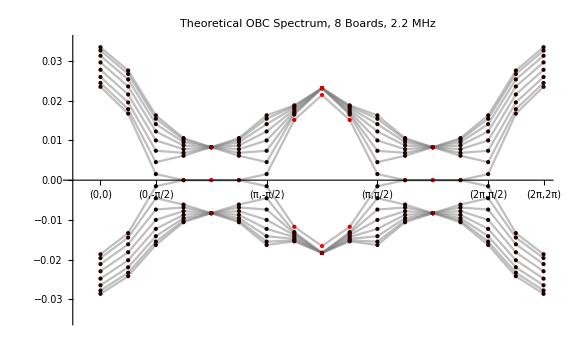
-Graphics-      (kx,ky)Laplacian Eigenvalues j_n

```mathematica
Labeled[Show[ListLinePlot[Transpose[HcPathTheory],PlotStyle->{Opacity[0.5,Gray]},Ticks->{{{1,"(0,0)"},{3,"(0,-π/2)"},{7,"(π,-π/2)"},{11,"(π,π/2)"},{15,"(2π,π/2)"},{17,"(2π,2π)"}},Automatic},PlotLabel->"Theoretical OBC Spectrum, "<>ToString[NverticalTheoryZ]<>" Boards, "<>ToString[frequency/(10^6)]<>" MHz",PlotRange->{-0.035,0.035},ImageSize->Large],Graphics[{PointSize[Medium],Flatten[HcPoints,{1,2}]},Axes->True,AspectRatio->1,TicksStyle->Directive[FontOpacity->10],Ticks->{{{p1Theory,"(0,0)"},{p2Theory,"(0,π/2)"},{p3Theory,"(π,π/2)"},{p4Theory,"(π,3π/2)"},{p5Theory,"(0,3π/2)"},{p6Theory,"(0,0"}},Automatic},ImageSize->Large,PlotLabel->"OBC Spectrum 8 Boards Theory",PlotRange->{All,All},AxesOrigin->{0,0}]],{"      (kx,ky)","Laplacian Eigenvalues \!\(\*SubscriptBox[\(j\), \(n\)]\)"},{Bottom,Left},RotateLabel->True]
```

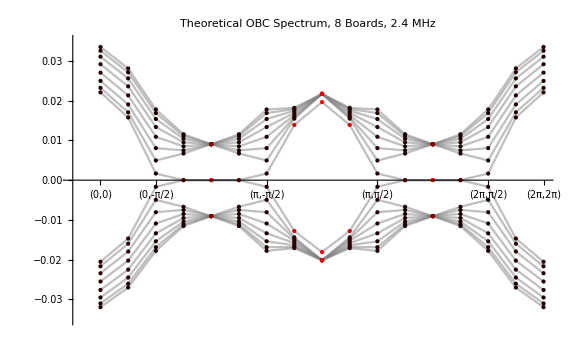
-Graphics-      (kx,ky)Laplacian Eigenvalues j_n

```mathematica
Labeled[Show[ListLinePlot[Transpose[HcPathTheory],PlotStyle->{Opacity[0.5,Gray]},Ticks->{{{1,"(0,0)"},{3,"(0,-π/2)"},{7,"(π,-π/2)"},{11,"(π,π/2)"},{15,"(2π,π/2)"},{17,"(2π,2π)"}},Automatic},PlotLabel->"Theoretical OBC Spectrum, "<>ToString[NverticalTheoryZ]<>" Boards, "<>ToString[frequency/(10^6)]<>" MHz",PlotRange->{-0.035,0.035},ImageSize->Large],Graphics[{PointSize[Medium],Flatten[HcPoints,{1,2}]},Axes->True,AspectRatio->1,TicksStyle->Directive[FontOpacity->10],Ticks->{{{p1Theory,"(0,0)"},{p2Theory,"(0,π/2)"},{p3Theory,"(π,π/2)"},{p4Theory,"(π,3π/2)"},{p5Theory,"(0,3π/2)"},{p6Theory,"(0,0"}},Automatic},ImageSize->Large,PlotLabel->"OBC Spectrum 8 Boards Theory",PlotRange->{All,All},AxesOrigin->{0,0}]],{"      (kx,ky)","Laplacian Eigenvalues \!\(\*SubscriptBox[\(j\), \(n\)]\)"},{Bottom,Left},RotateLabel->True]
```

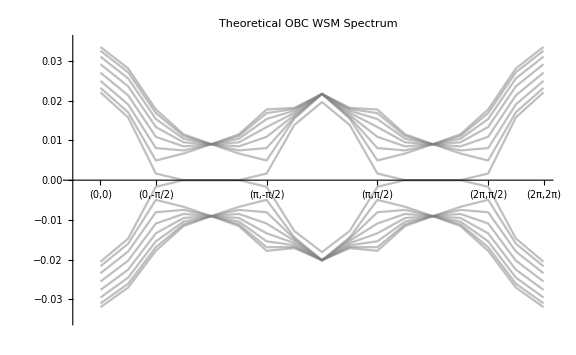
-Graphics-      (kx,ky)Laplacian Eigenvalues j_n

-Graphics-      (kx,ky)Laplacian Eigenvalues j_n

```mathematica
Labeled[ListLinePlot[Transpose[HcPathTheory],PlotStyle->{Opacity[0.5,Gray]},Ticks->{{{1,"(0,0)"},{3,"(0,-π/2)"},{7,"(π,-π/2)"},{11,"(π,π/2)"},{15,"(2π,π/2)"},{17,"(2π,2π)"}},Automatic},PlotLabel->"Theoretical OBC WSM Spectrum",PlotRange->{-0.035,0.035},ImageSize->Large],{"      (kx,ky)","Laplacian Eigenvalues \!\(\*SubscriptBox[\(j\), \(n\)]\)"},{Bottom,Left},RotateLabel->True]
```